## All edges

```mathematica
Column[
Table[
Labeled[
With[
{relevant = Select[Keys[allGraphs4],With[{g=allGraphs4[#,"graph"]},VertexCount[g]==4 && EdgeCount[g]==edges]&]},
TableForm[
Sort[
Tally[
Table[
{Sort[Tally[Map[StringCount[SymbolName[#],"x"]+1&,ListofVars[allGraphs4[k,"colofour"]]]]],Labeled[allGraphs4[k,"graph"],k]},
{k,relevant}
]
,#1[[1]]==#2[[1]]&
]
], TableDepth->1]
],
Style[edges,Red,48,Bold],
Top
],
{edges,0,6}
]
]
```

{{{{1,1},{2,7},{3,6},{4,1}},-Graphics-0},1}0
{{{{2,4},{3,5},{4,1}},-Graphics-243},6}1
{{{{2,2},{3,4},{4,1}},-Graphics-324},15}2
{{{{3,3},{4,1}},-Graphics-333},4}
{{{{2,1},{3,3},{4,1}},-Graphics-351},16}3
{{{{3,2},{4,1}},-Graphics-360},12}
{{{{2,1},{3,2},{4,1}},-Graphics-328},3}4
{{{{3,1},{4,1}},-Graphics-363},6}5
{{{{4,1}},-Graphics-364},1}6

```mathematica
PaintEdges[key_,key2_,allGraphs_]:=Block[{
form=allGraphs[key,"colofourrealnull"],
form2=allGraphs[key2, "colofourrealnull"],
form3=Map[ChangeSymbol[#]&,allGraphs[key2,"colofour"]],pairs, vars, blocks=Association[],c,edges,edges2,set, found=Association[],realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],nonRoot,   blueEdges, blueVertices, g, edgeSymbols, otherEdges, labels, nodes,
colors={Lighter[Red],Red,Darker[Red],Darker[Darker[Red]],Darker[Darker[Darker[Red]]]}},
edgeSymbols=Select[ListofVars[form2],StringCount[SymbolName[#],"x"]==2&];
vars=ListofVars[form];
Table[blocks[k]={},{k,0,5}];
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,5}];
pairs=Subsets[ListofVars[form3],{2}];
edges2={};
Table[With[{e=DirectedEdge[
p[[2]],
p [[1]]]},
If[MemberQ[edges,e],edges2=Append[edges2,e]]],{p,pairs}
];
g=Graph[vars,edges];
blueEdges=edges2;
blueVertices=Map[#[[2]]&,blueEdges];
otherEdges=Flatten[Join[Table[Descendents[g,{e}],{e,edgeSymbols}]]];
labels=Map[#[[1]]->Style[ #[[2]],Bold]&,Tally[otherEdges]];
nodes=Map[#[[1,1]]-> Part[colors,#[[2]]]&,Tally[otherEdges]];
otherEdges=Map[#[[1]]-> Part[colors,#[[2]]]&,Tally[otherEdges]];
Graph[vars,edges,
VertexLabels->Table[n->Rotate[SymbolToLabel[n],Pi/4],{n,vars}],
GraphLayout->"LayeredDigraphEmbedding",
EdgeStyle->otherEdges,
EdgeLabels->labels,
VertexStyle->Join[nodes,Map[#->Cyan&,blueVertices]],
ImageSize->720]
]
```

```mathematica
allGraphs4[360,"graph"]
```

-Graphics-

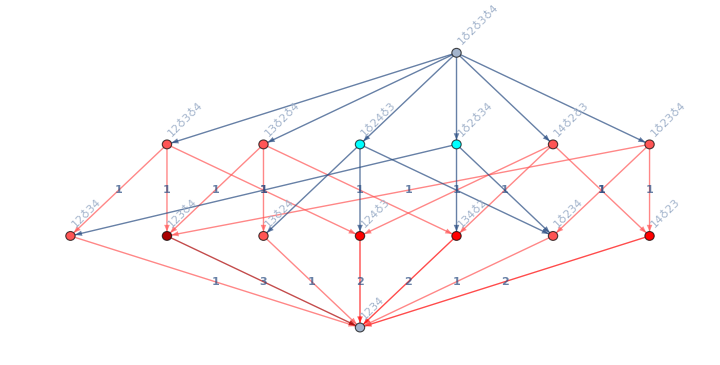

```mathematica
PaintEdges[K4Key, 360, allGraphs4]
```

```mathematica
allGraphs4[328,"graph"]
```

-Graphics-

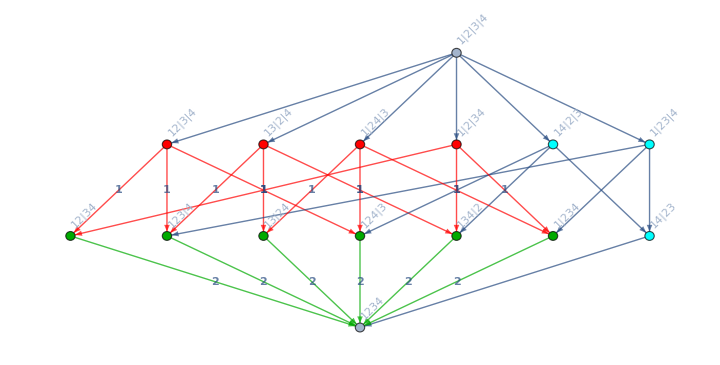

```mathematica
PaintEdges[K4Key, 328, allGraphs4]
```